```mathematica
data = {
(*{2000, 0.1, Around[7.72,0.46]},
{2000, 0.5, Around[13.12,3.78]},
{2000, 1, Around[23.25,6.52]},

{1000, 0.1, Around[7.39,3.09]},
{1000, 0.5, Around[15.92,4.21]},
{1000, 1, Around[25.05,7.98]},

{500, 0.1, Around[7.37,2.03]},
{500, 0.5, Around[15.07,4.03]},
{500, 1, Around[22.84,10.78]},

{200, 0.1, Around[7.40,1.74]},
{200, 0.5, Around[17.66,2.98]},
{200, 1, Around[25.59,5.51]},

{100, 0.1, Around[8.74,3.09]},
{100, 0.5, Around[15.87,2.91]},
{100, 1, Around[24.02,0.71]}*)

{5000,0.1,Around[7.64,1.51]},
{5000,0.5,Around[12.79,1.63]},
{5000,1.0,Around[21.48,2.43]},

{2000,0.1,Around[7.96,0.47]},
{2000,0.5,Around[13.34,3.70]},
{2000,1.0,Around[23.57,7.23]},

{1000,0.1,Around[7.54,3.29]},
{1000,0.5,Around[15.82,4.19]},
{1000,1.0,Around[25.97,8.54]},

{500,0.1,Around[7.71,2.03]},
{500,0.5,Around[15.25,4.39]},
{500,1.0,Around[24.01,11.13]},

{200,0.1,Around[7.69,1.90]},
{200,0.5,Around[18.66,4.19]},

{100,0.5,Around[15.95,2.94]},

{50,0.1,Around[8.39,1.90]},
{50,0.5,Around[29.44,7.46]},

{20,0.1,Around[13.28,1.13]},
{20,0.5,Around[41.82,7.74]},

{10,0.5,Around[41.41,9.65]},

{2,0.1,Around[14.91,2.57]}
}
```

{{5000,0.1,7.61.5},{5000,0.5,12.81.6},{5000,1.,21.52.4},{2000,0.1,8.00.5},{2000,0.5,13.4.},{2000,1.,24.7.},{1000,0.1,7.53.3},{1000,0.5,16.4.},{1000,1.,26.9.},{500,0.1,7.72.0},{500,0.5,15.4.},{500,1.,24.11.},{200,0.1,7.71.9},{200,0.5,19.4.},{100,0.5,16.02.9},{50,0.1,8.41.9},{50,0.5,29.7.},{20,0.1,13.31.1},{20,0.5,42.8.},{10,0.5,41.10.},{2,0.1,14.92.6}}

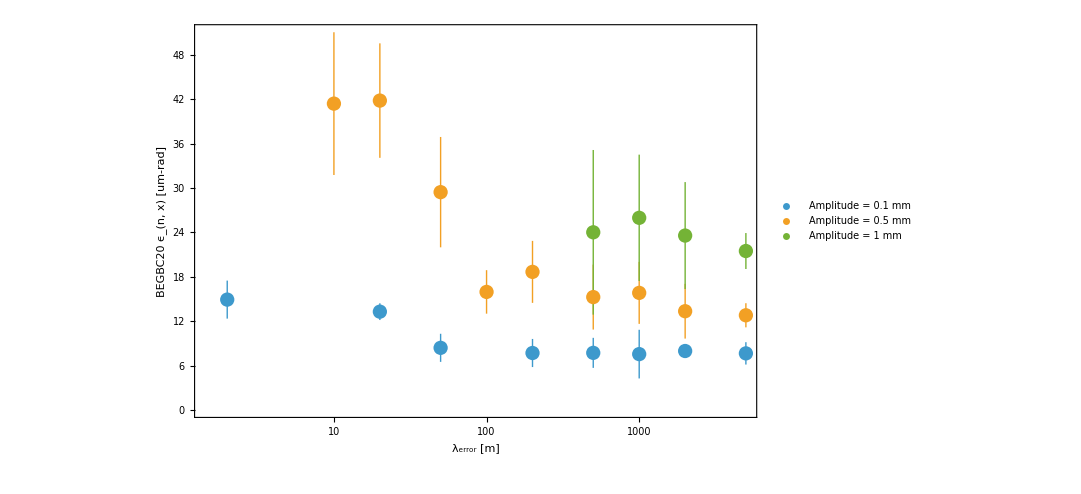

```mathematica
ListLogLinearPlot[
Values[GroupBy[data,#[[2]]&]][[All,All,{1,3}]],
ImageSize->800,
LabelStyle->20,
FrameLabel->{"λ_error [m]", "BEGBC20 ϵ_(n, x) [um-rad]"},
Frame->True,
PlotLegends->Placed[{"Amplitude = 0.1 mm","Amplitude = 0.5 mm","Amplitude = 1 mm"},{0.85,0.85}]
]
```